# Mathematica Project (1) - Ty Limpasuvan

## (1)

```mathematica
(* I will be using the Erdos-Renyi method for generating graphs *)
(* This function receives arguments n (dimensions) and p (probability of adding an edge to graph) and returns the adjacency matrix of a generated graph *)
GetAdjacency[n_, p_]:=
Module [{mat = ConstantArray[0,{n, n}], ran = RandomGraph[BernoulliGraphDistribution[n, p]]},
mat = AdjacencyMatrix[ran];
mat]
```

## (2)

```mathematica
(* Estimates the probability of generating connected graphs.  Accepts the arguments n (dimensions of adjacency matrix), p (probability of adding an edge to a graph) and m (number of graphs to be generated) *)
GetConnectionProbability[n_, p_, m_] :=
Module[{count = 0, total = 0},
(* Generate m random graphs *)
While[total < m,
temp = AdjacencyGraph[GetAdjacency[n,p]];
(* Increase the count of the connected graphs if the generated graph is connected *)
If[ConnectedGraphQ[temp],count+= 1];
(* Increment the total regardless of whether the graph is connected *)
total += 1;
];
(* Find the fraction of the generated graphs that were connected and return it *)
count / total
]
```

## (3)

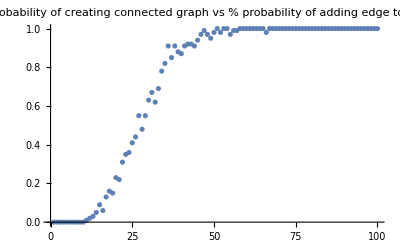

```mathematica
(* For showing the critical value of p, I generate 100 graphs and have an n x n adjacency matrix for each calculation. *)
mtest = 100;
ntest=10;
rangeP = Table[{i, GetConnectionProbability[ntest, i / 100, mtest]}, {i, 1, 100}];
(* After calling my function on the the range of values from 0 to 1 for the probability of adding an edge to a graph, I plot my results *)
ListPlot[rangeP, PlotLabel->"Probability of creating connected graph \nvs % probability of adding edge to graph"]
```